```mathematica
Quit[]
```

# initial conditions

```mathematica
m1=1.5;m2=1;G=1; λmax=2 ; λ0=0; (* flow amount and initial lambda *)
Q1=(2+3 m2/(2 m1));Q2=(2+3 m1/(2 m2));

Jinit={0,0,1}; (* J aligned along z and stays conserved *)
Rinit={1,.5,1.5};
Pinit={1,-4,1};
Linit=Cross[Rinit, Pinit];
S1init={1,1,1.3}
S2init=Jinit-Linit -S1init
RN=Norm[Rinit];
PN=Norm[Pinit];
S1N = Norm[S1init] ;    
S2N = Norm[S2init] ;
LN=Norm[Linit] ;
JN=Norm[Jinit];





(*RP space initial angles *)
f0=(S1init.S2init)/(Q1-Q2);
ϕL0=ArcTan[Linit[[1]],Linit[[2]]];
acos[k_,a_,b_]:= If[k.(a×b)>0,VectorAngle[a,b],2π-VectorAngle[a,b]];
ϕR0=acos[Linit, Cross[Jinit , Linit],Rinit];
ϕP0=acos[Linit, Cross[Jinit , Linit],Pinit];

(*subspin sector : here we find a candidate (R1, P1) and (R2,P2) whose cross products give initial S1 and S2 vectors*)

(*subspin space initial angles for S1 *)
X1=Cross[Jinit,S1init];
Y1=Cross[S1init,X1];
R1init={rx,ry,rz}/.Solve[Cross[{rx,ry,rz},{px,py,pz}]==S1init,{px,py,pz,rx,ry,rz}][[2]]/.{ry->1,py->1};
P1init={px,py,pz}/.Solve[Cross[{rx,ry,rz},{px,py,pz}]==S1init,{px,py,pz,rx,ry,rz}][[2]]/.{ry->1,py->1};
R1N=Norm[R1init]; P1N=Norm[P1init];
Cross[R1init,P1init]

ϕS10=ArcTan[S1init[[1]],S1init[[2]]];
ϕR10=acos[S1init, X1,R1init];
ϕP10=acos[S1init, X1,P1init];

(*subspin space initial angles for S2 *)
X2=Cross[Jinit,S2init];
Y2=Cross[S2init,X2];
R2init={rx,ry,rz}/.Solve[Cross[{rx,ry,rz},{px,py,pz}]==S2init,{px,py,pz,rx,ry,rz}][[2]]/.{ry->1,py->1}; P2init={px,py,pz}/.Solve[Cross[{rx,ry,rz},{px,py,pz}]==S2init,{px,py,pz,rx,ry,rz}][[2]]/.{ry->1,py->1};
R2N=Norm[R2init];  P2N=Norm[P2init];
Cross[R2init,P2init]

ϕS20=ArcTan[S2init[[1]],S2init[[2]]];
ϕR20=acos[S2init, X2,R2init];
ϕP20=acos[S2init, X2,P2init];
```

{1,1,1.3}

{-7.5,-1.5,4.2}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{1.,1.,1.3}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-7.5,-1.5,4.2}

# Variables and Conserved quantities

```mathematica
R = {Rx, Ry,Rz} ; P ={Px,Py,Pz};
S1= {S1x, S1y,S1z} ;    S2= {S2x, S2y,S2z} ;
Seff= Q1 S1+ Q2 S2;
L=Cross[R,P] ;
SeffL= Seff.L ;
```

# some parameters determined from initial data

```mathematica
Δ1=(1/(Q1-Q2))((1/2)(Jn^2-Ln^2-S1n^2-S2n^2)-SeffL/Q2 );
Δ2=(1/(Q1-Q2))((1/2)(Jn^2-Ln^2-S1n^2-S2n^2)-SeffL/Q1 );
Δ21=SeffL/(Q1 Q2 );
Σ1=((Q1-Q2) Δ1)/(S1n * S2n);
Σ2= SeffL/( Q2 * Ln* S2n );a3 =2 Q1 Q2(Q2-Q1);a2=2(Δ1+Δ2)(Q1-Q2)Q1 Q2- Ln^2(Q1-Q2)^2 -Q1^2 S1n^2-Q2^2 S2n^2;
a1=2(Q1^2 S1n^2 Δ2+Q2^2 S2n^2 Δ1+Q1 Q2 Δ1 Δ2 (Q2-Q1));
a0=Ln^2 S1n^2 S2n^2-Q1^2 S1n^2 Δ2^2-Q2^2 S2n^2 Δ1^2;


A=2 Q1 Q2(Q2-Q1);
p=(3 a1 a3 -a2^2)/(3 a3^2); 
q=(2 a2^3-9 a1 a2 a3+27 a0 a3^2)/(27 a3^3);
f1=-a2/(3 a3)+2 √(-p/3)Cos[1/3 ArcCos[(3 q)/(2p)√(-3/p)]+(2 π)/3];f2=-a2/(3 a3)+2 √(-p/3)Cos[1/3 ArcCos[(3 q)/(2p)√(-3/p)]+(2*2 π)/3] ;f3=-a2/(3 a3)+2 √(-p/3)Cos[1/3 ArcCos[(3 q)/(2p)√(-3/p)]+(3*2 π)/3];

k=(f2-f1)/(f3-f1);
α=2/(√(A(f3-f1)))EllipticF[ArcSin[√((f0-f1)/(f2-f1))],k];




B1=(1/2)((SeffL +Ln^2(Q1+Q2))(Jn+Ln)+Ln(Q1  S1n^2+Q2  S2n^2+(Q1+Q2)(Δ2 Q1 -Δ1 Q2)));B2=(1/2)((SeffL +Ln^2(Q1+Q2))(Jn-Ln)-Ln(Q1  S1n^2+Q2  S2n^2+(Q1+Q2)(Δ2 Q1 -Δ1 Q2)));D1=Ln(Ln+Jn)+(Δ2 Q1 -Δ1 Q2);D2=Ln(Ln-Jn)+(Δ2 Q1 -Δ1 Q2);


α1sq=((-f1+f2) (Q1-Q2))/(D1+f1 (-Q1+Q2)); α2sq=((-f1+f2) (Q1-Q2))/(D2+f1 (-Q1+Q2));


(*subspin space for spin S1*)
B1s1=1/2(-S1n Q1 (Ln^2 -Jn S1n + S1n^2 +Δ2 Q1)+(Jn-S1n)^2 S1n Q2-(Jn-2S1n)Δ1 Q1 Q2 +(Jn-S1n)Δ1 Q2^2);
B2s1=1/2(S1n Q1 (Ln^2 +Jn S1n + S1n^2 +Δ2 Q1)-(Jn+S1n)^2 S1n Q2-(Jn+2S1n)Δ1 Q1 Q2 +(Jn+S1n)Δ1 Q2^2);
D1s1=(S1n-Jn)S1n - Δ1 Q2;
D2s1=(S1n+Jn)S1n - Δ1 Q2;


α1s1sq=((-Q1)(f2-f1))/(D1s1+f1 Q1); α2s1sq=((-Q1)(f2-f1))/(D2s1+f1 Q1);
```

# numerical solutions

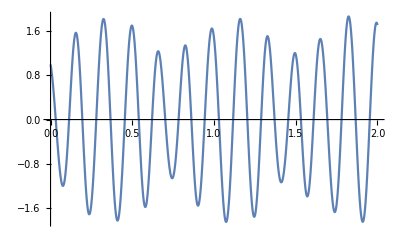
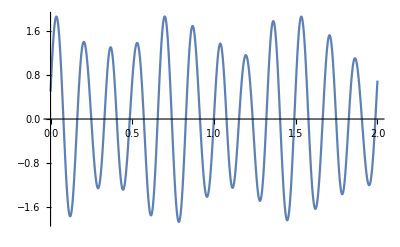
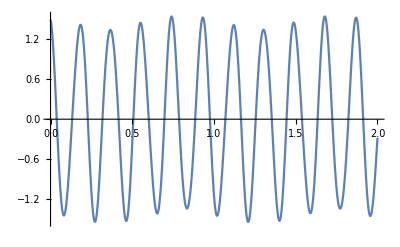
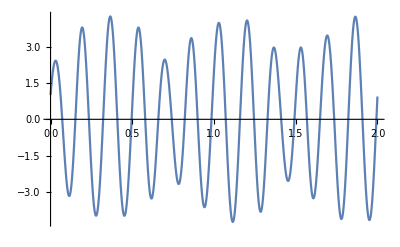
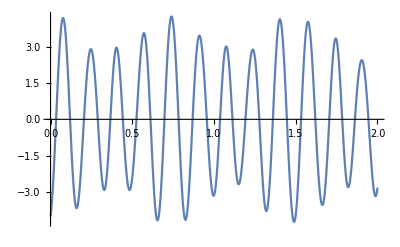
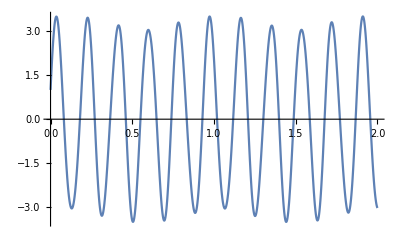
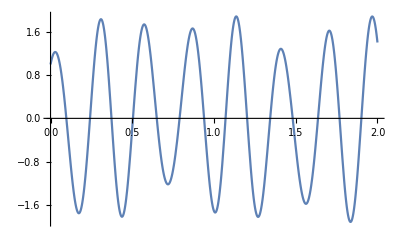
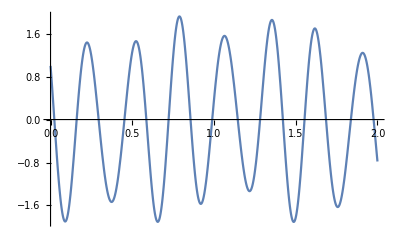
```mathematica
rxnumeric=-Graphics-; rynumeric=-Graphics-; rznumeric=-Graphics-;
pxnumeric=-Graphics-;pynumeric=-Graphics-; pznumeric=-Graphics-;
s1xnumeric=-Graphics-;s1ynumeric=-Graphics-; s1znumeric=-Graphics-;
s2xnumeric=-Graphics-;s2ynumeric=-Graphics-; s2znumeric=-Graphics-;
fnumeric=-Graphics-;phiLnumeric=-Graphics-; phinumeric=-Graphics-;
```

# solution of angles in R,P space

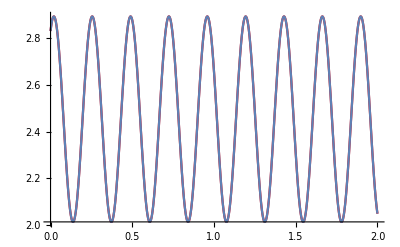

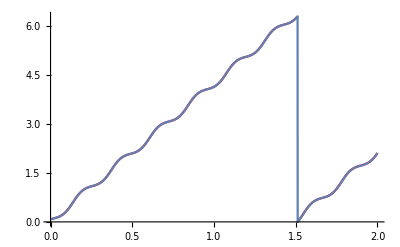

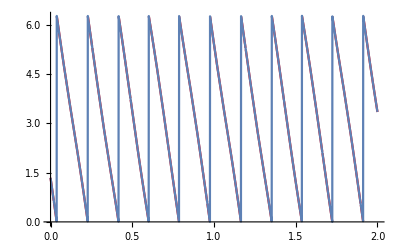

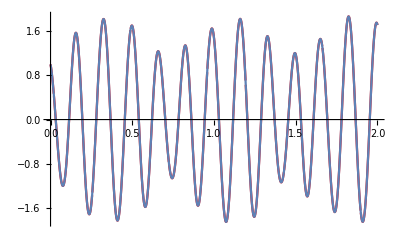

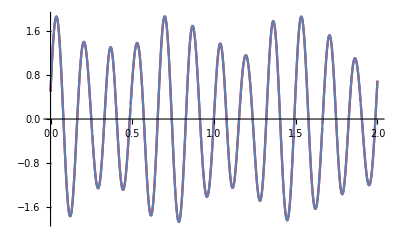

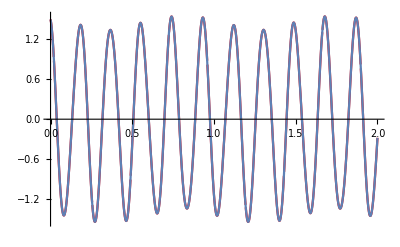

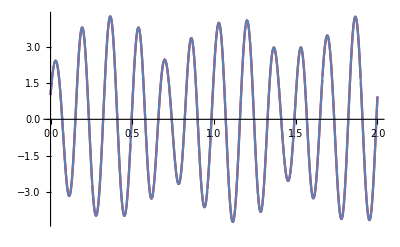

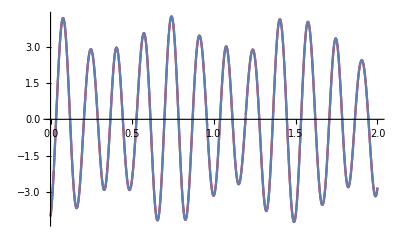

```mathematica
{Rx,Ry,Rz} = Rinit  ;
{Px,Py,Pz}=Pinit  ;
{S1x,S1y,S1z} = S1init ; 
{S2x,S2y,S2z} = S2init  ;
 Rn=RN; Pn=PN;S1n=S1N;S2n=S2N; Ln=LN;Jn=JN;

f=f1+(f2-f1)(JacobiSN[1/2 √(A(f3-f1))(α+(λ-λ0)),k])^2;





(*γ=JacobiAmplitude[1/2 √(A (-f1+f3)) (λ-λ0)+EllipticF[ArcSin[√((-f0+f1)/(f1-f2))],k],k];*) (*in paper we call it ϕp but changed it to β to avoid confusion with ϕ azimuth angle of P vector*)
(*Following expressions are worked out in phiexpressions_seffl.nb*)

ϕL=ϕL0-(2 ((B1 EllipticPi[α1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D1+f1 (-Q1+Q2))+(B2 EllipticPi[α2sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D2+f1 (-Q1+Q2))))/(√(A (-f1+f3)))+(2 ((B1 EllipticPi[α1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k])/(D1+f1 (-Q1+Q2))+(B2 EllipticPi[α2sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k])/(D2+f1 (-Q1+Q2))))/(√(A (-f1+f3)));






ϕR=-((Ln^2 (Q1+Q2)+SeffL+Q1 Q2 (Δ1-Δ2)) (λ-λ0))/Ln+ϕR0-(2 ((B1 EllipticPi[α1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D1+f1 (-Q1+Q2))-(B2 EllipticPi[α2sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D2+f1 (-Q1+Q2))))/(√(A (-f1+f3)))+(2 ((B1 EllipticPi[α1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k])/(D1+f1 (-Q1+Q2))-(B2 EllipticPi[α2sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k])/(D2+f1 (-Q1+Q2))))/(√(A (-f1+f3)));

ϕP=-((Ln^2 (Q1+Q2)+SeffL+Q1 Q2 (Δ1-Δ2)) (λ-λ0))/Ln+ϕP0-(2 ((B1 EllipticPi[α1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D1+f1 (-Q1+Q2))-(B2 EllipticPi[α2sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D2+f1 (-Q1+Q2))))/(√(A (-f1+f3)))+(2 ((B1 EllipticPi[α1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k])/(D1+f1 (-Q1+Q2))-(B2 EllipticPi[α2sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k])/(D2+f1 (-Q1+Q2))))/(√(A (-f1+f3)));


Show[Plot[f,{λ,0,λmax},PlotStyle->Red],fnumeric]
Show[Plot[Mod[ϕL,2π],{λ,0,λmax},PlotStyle->Red],phiLnumeric]
Show[Plot[Mod[ϕR,2π],{λ,0,λmax},PlotStyle->Red],phinumeric]


Emat={{-Sin[ϕL],Cos[ϕL],0},{-((Ln^2+f (-Q1+Q2)+S1n S2n Σ1+Ln S2n Σ2) Cos[ϕL])/(Jn Ln),-((Ln^2+f (-Q1+Q2)+S1n S2n Σ1+Ln S2n Σ2) Sin[ϕL])/(Jn Ln),√((Jn^2 Ln^2-(Ln^2+f (-Q1+Q2)+S1n S2n Σ1+Ln S2n Σ2)^2)/(Jn^2 Ln^2))},{√((Jn^2 Ln^2-(Ln^2+f (-Q1+Q2)+S1n S2n Σ1+Ln S2n Σ2)^2)/(Jn^2 Ln^2)) Cos[ϕL],√((Jn^2 Ln^2-(Ln^2+f (-Q1+Q2)+S1n S2n Σ1+Ln S2n Σ2)^2)/(Jn^2 Ln^2)) Sin[ϕL],(Ln^2-f Q1+f Q2+S1n S2n Σ1+Ln S2n Σ2)/(Jn Ln)}};


Rfinal=Flatten[Inverse[Emat].({{Rn Cos[ϕR]}, {Rn Sin[ϕR]}, {0}})] (* in inertial frame*);
Pfinal=Flatten[Inverse[Emat].({{Pn Cos[ϕP]}, {Pn Sin[ϕP]}, {0}})] (* in inertial frame*);
Lfinal=Cross[Rfinal,Pfinal];

Show[Plot[Rfinal[[1]],{λ,λ0,λmax},PlotStyle->{Red}],rxnumeric]
Show[Plot[Rfinal[[2]],{λ,λ0,λmax},PlotStyle->{Red}],rynumeric]
Show[Plot[Rfinal[[3]],{λ,λ0,λmax},PlotStyle->{Red}],rznumeric]
Show[Plot[Pfinal[[1]],{λ,λ0,λmax},PlotStyle->{Red}],pxnumeric]
Show[Plot[Pfinal[[2]],{λ,λ0,λmax},PlotStyle->{Red}],pynumeric]
Show[Plot[Pfinal[[3]],{λ,λ0,λmax},PlotStyle->{Red}],pznumeric]

Clear[Rx, Ry, Rz, Px, Py, Pz, S1x, S1y, S1z, S2x, S2y, S2z,Rn,Pn,S1n,S2n,Jn,Ln,R1n,P1n,R2n,P2n]
```

# solution in subspin space

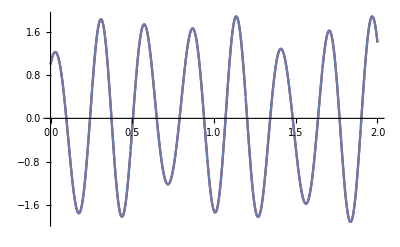

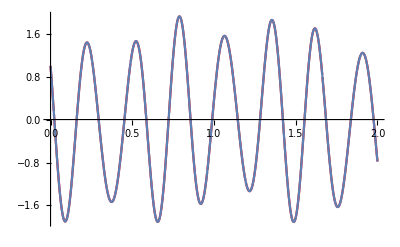

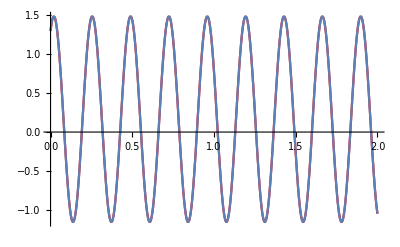

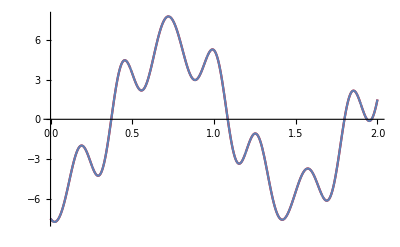

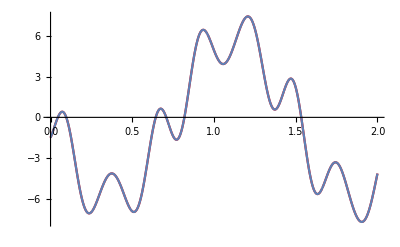

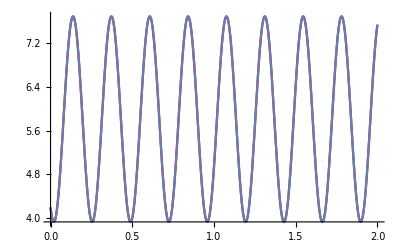

```mathematica
{Rx,Ry,Rz} = Rinit  ;
{Px,Py,Pz}=Pinit  ;
{S1x,S1y,S1z} = S1init ; 
{S2x,S2y,S2z} = S2init  ;
 Rn=RN; Pn=PN;S1n=S1N;S2n=S2N; 
Ln=LN;Jn=JN; R1n=R1N; P1n=P1N;







ϕS1=Jn Q2 (λ-λ0)+ϕS10-(2 ((B1s1 EllipticPi[α1s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D1s1+f1 Q1)+(B2s1 EllipticPi[α2s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D2s1+f1 Q1)))/(√(A (-f1+f3)))+(2 (B1s1 (D2s1+f1 Q1) EllipticPi[α1s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k]+B2s1 (D1s1+f1 Q1) EllipticPi[α2s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k]))/(√(A (-f1+f3)) (D1s1+f1 Q1) (D2s1+f1 Q1));






ϕR1=(-Q1+Q2) S1n (λ-λ0)+ϕR10+(2 ((B1s1 EllipticPi[α1s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D1s1+f1 Q1)-(B2s1 EllipticPi[α2s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D2s1+f1 Q1)))/(√(A (-f1+f3)))+(-2 B1s1 (D2s1+f1 Q1) EllipticPi[α1s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k]+2 B2s1 (D1s1+f1 Q1) EllipticPi[α2s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k])/(√(A (-f1+f3)) (D1s1+f1 Q1) (D2s1+f1 Q1));

ϕP1=(-Q1+Q2) S1n (λ-λ0)+ϕP10+(2 ((B1s1 EllipticPi[α1s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D1s1+f1 Q1)-(B2s1 EllipticPi[α2s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) α,k],k])/(D2s1+f1 Q1)))/(√(A (-f1+f3)))+(-2 B1s1 (D2s1+f1 Q1) EllipticPi[α1s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k]+2 B2s1 (D1s1+f1 Q1) EllipticPi[α2s1sq,JacobiAmplitude[1/2 √(A (-f1+f3)) (α+λ-λ0),k],k])/(√(A (-f1+f3)) (D1s1+f1 Q1) (D2s1+f1 Q1));



EmatS1={{-Sin[ϕS1],Cos[ϕS1],0},{-((f Q1 (Q1-Q2)+S1n (Q1 S1n-Q2 (S1n+S2n Σ1))) Cos[ϕS1])/(Jn (Q1-Q2) S1n),-((f Q1 (Q1-Q2)+S1n (Q1 S1n-Q2 (S1n+S2n Σ1))) Sin[ϕS1])/(Jn (Q1-Q2) S1n),√(1-(f Q1 (Q1-Q2)+S1n (Q1 S1n-Q2 (S1n+S2n Σ1)))^2/(Jn^2 (Q1-Q2)^2 S1n^2))},{√(1-(f Q1 (Q1-Q2)+S1n (Q1 S1n-Q2 (S1n+S2n Σ1)))^2/(Jn^2 (Q1-Q2)^2 S1n^2)) Cos[ϕS1],√(1-(f Q1 (Q1-Q2)+S1n (Q1 S1n-Q2 (S1n+S2n Σ1)))^2/(Jn^2 (Q1-Q2)^2 S1n^2)) Sin[ϕS1],((f Q1)/S1n+(Q1 S1n-Q2 (S1n+S2n Σ1))/(Q1-Q2))/Jn}};


R1final=Flatten[Inverse[EmatS1].({{R1n Cos[ϕR1]}, {R1n Sin[ϕR1]}, {0}})] (* in inertial frame*);
P1final=Flatten[Inverse[EmatS1].({{P1n Cos[ϕP1]}, {P1n Sin[ϕP1]}, {0}})] (* in inertial frame*);
S1final=Cross[R1final,P1final];
S2final=Jinit-Lfinal-S1final;


(*Plot[ϕS1,{λ,0,λmax},PlotStyle->{Red}]
Plot[ϕR1,{λ,0,λmax},PlotStyle->{Red}]
Plot[ϕP1,{λ,0,λmax},PlotStyle->{Red}]
Plot[R1final,{λ,0,λmax}]
Plot[P1final,{λ,0,λmax}]
Plot[S1final,{λ,0,λmax}]*)

Show[Plot[S1final[[1]],{λ,0,λmax},PlotStyle->{Red}],s1xnumeric]
Show[Plot[S1final[[2]],{λ,0,λmax},PlotStyle->{Red}],s1ynumeric]
Show[Plot[S1final[[3]],{λ,0,λmax},PlotStyle->{Red}],s1znumeric]

Show[Plot[S2final[[1]],{λ,0,λmax},PlotStyle->{Red}],s2xnumeric]
Show[Plot[S2final[[2]],{λ,0,λmax},PlotStyle->{Red}],s2ynumeric]
Show[Plot[S2final[[3]],{λ,0,λmax},PlotStyle->{Red}],s2znumeric]


Clear[Rx, Ry, Rz, Px, Py, Pz, S1x, S1y, S1z, S2x, S2y, S2z, m1, m2,Q1,Q2,Rn,Pn,S1n,S2n,Jn,Ln,R1n,P1n,R2n,P2n]
```